Target export directory: G:\物理实用编程 2025秋季学期 期末考试\Part1_MMA\

--- Visualizing Potential and Field Lines ---

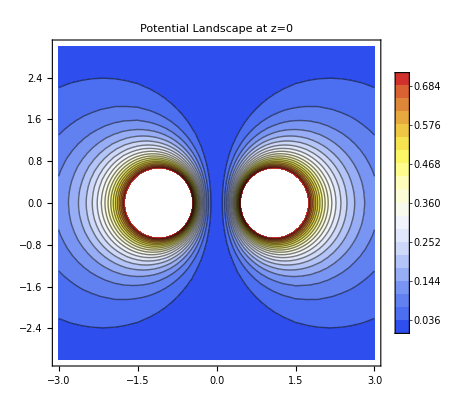

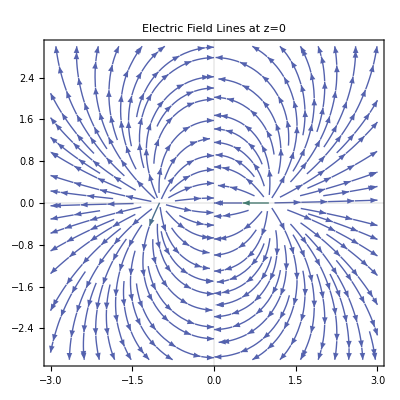

Finding equilibrium points (Optimized Symbolic Search)...

Equilibrium points (E=0): y→0 | z→-0.620721 | x→0
y→0 | z→-0.620721 | x→0
y→0 | z→-0.620721 | x→0
y→0 | z→-0.620721 | x→0

--- Task 2 Completed ---

```mathematica
(* ===MMA 任务二：静电场数值模拟 (独立运行版)===*)ClearAll["Global`*"];

(*1. 环境配置*)
exportDir=If[Quiet[NotebookFileName[]]=!=$Failed,NotebookDirectory[],$HomeDirectory];
Print["Target export directory: ",exportDir];

(*2. 电荷定义*)
q=1;k=1;
charges={{q,{1,0,0}},{q,{-1,0,0}},{-2*q,{0,0,1}}};

(*3. 电势与电场定义*)
phiTotal[x_,y_,z_]:=Sum[c[[1]]/Sqrt[(x-c[[2,1]])^2+(y-c[[2,2]])^2+(z-c[[2,3]])^2],{c,charges}];

fieldE[x_,y_,z_]:=-Grad[phiTotal[sx,sy,sz],{sx,sy,sz}]/. {sx->x,sy->y,sz->z};

(*4. 平面可视化 (z=0)*)
Print["--- Visualizing Potential and Field Lines ---"];
contourPlot=ContourPlot[phiTotal[x,y,0],{x,-3,3},{y,-3,3},Contours->20,ColorFunction->"TemperatureMap",PlotLabel->"Potential Landscape at z=0",PlotTheme->"Detailed"];

streamPlot=StreamPlot[Take[fieldE[x,y,0],2],{x,-3,3},{y,-3,3},PlotLabel->"Electric Field Lines at z=0",PlotTheme->"Scientific"];

(*显式显示图像*)
Show[contourPlot]
Show[streamPlot]

(*5. 符号优化与平衡点求解*)
Print["Finding equilibrium points (Optimized Symbolic Search)..."];
symbolicPhi=phiTotal[sx,sy,sz];
symbolicE=-Grad[symbolicPhi,{sx,sy,sz}]//Simplify;

(*Solve using the pre-computed symbolic expressions*)
eqPoints=NSolve[Thread[(symbolicE/. {sx->x,sy->y,sz->z})==0]~Join~{-2<x<2,-2<y<2,-2<z<2},{x,y,z},Reals];

Print["Equilibrium points (E=0): ",eqPoints//TableForm];
Print["\n--- Task 2 Completed ---"];
```